# CV:QCQ vs CV:CCQ vs DV SKR analysis

```mathematica
VABERF=({{1+2 μ, 2 √η √(μ (1+μ)), -2 √(1-η) √κ √(μ (1+μ)), 0, 2 √(1-η) √(1-κ) √(μ (1+μ)), 0, 0, 0, 0, 0}, {2 √η √(μ (1+μ)), 1-2 ne (-1+η)+2 η μ, 2 √(-(-1+η) η) √κ (ne-μ), 2 √(ne (1+ne)) √(1-η), 2 √(-(-1+η) η) √(1-κ) (-ne+μ), 0, 0, 0, 0, 0}, {-2 √(1-η) √κ √(μ (1+μ)), 2 √(-(-1+η) η) √κ (ne-μ), 1+2 κ (ne η+μ-η μ), 2 √(ne (1+ne)) √η √κ, -2 √(-(-1+κ) κ) (ne η+μ-η μ), 0, 0, 0, 0, 0}, {0, 2 √(ne (1+ne)) √(1-η), 2 √(ne (1+ne)) √η √κ, 1+2 ne, -2 √(ne (1+ne)) √η √(1-κ), 0, 0, 0, 0, 0}, {2 √(1-η) √(1-κ) √(μ (1+μ)), 2 √(-(-1+η) η) √(1-κ) (-ne+μ), -2 √(-(-1+κ) κ) (ne η+μ-η μ), -2 √(ne (1+ne)) √η √(1-κ), 1-2 ne η (-1+κ)+2 (-1+η) (-1+κ) μ, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 1+2 μ, -2 √η √(μ (1+μ)), 2 √(1-η) √κ √(μ (1+μ)), 0, -2 √(1-η) √(1-κ) √(μ (1+μ))}, {0, 0, 0, 0, 0, -2 √η √(μ (1+μ)), 1-2 ne (-1+η)+2 η μ, 2 √(-(-1+η) η) √κ (ne-μ), -2 √(ne (1+ne)) √(1-η), 2 √(-(-1+η) η) √(1-κ) (-ne+μ)}, {0, 0, 0, 0, 0, 2 √(1-η) √κ √(μ (1+μ)), 2 √(-(-1+η) η) √κ (ne-μ), 1+2 κ (ne η+μ-η μ), -2 √(ne (1+ne)) √η √κ, -2 √(-(-1+κ) κ) (ne η+μ-η μ)}, {0, 0, 0, 0, 0, 0, -2 √(ne (1+ne)) √(1-η), -2 √(ne (1+ne)) √η √κ, 1+2 ne, 2 √(ne (1+ne)) √η √(1-κ)}, {0, 0, 0, 0, 0, -2 √(1-η) √(1-κ) √(μ (1+μ)), 2 √(-(-1+η) η) √(1-κ) (-ne+μ), -2 √(-(-1+κ) κ) (ne η+μ-η μ), 2 √(ne (1+ne)) √η √(1-κ), 1-2 ne η (-1+κ)+2 (-1+η) (-1+κ) μ}});
```

### CV Basics

```mathematica
SymplecticForm[n_]:=ArrayFlatten[TensorProduct[{{0,1},{-1,0}},IdentityMatrix[n]],2];
```

```mathematica
CovVac[n_]:=IdentityMatrix[2n];(*Covariance Matrix of a n-mode vacuum state*)
```

```mathematica
CovTMSV[μ_]:=({{2μ+1, 2 √(μ(μ+1)), 0, 0}, {2 √(μ(μ+1)), 2μ+1, 0, 0}, {0, 0, 2μ+1, -2 √(μ(μ+1))}, {0, 0, -2 √(μ(μ+1)), 2μ+1}});(*Covariance Matrix of a TMSV state, where λ = Tanh[r], μ = λ^2/(1-λ^2) = Sinh^2[r] is the average photon number in each mode and r is the squeezing parameter*)
```

```mathematica
BsSymp[t_]:=({{√t, √(1-t), 0, 0}, {-√(1-t), √t, 0, 0}, {0, 0, √t, √(1-t)}, {0, 0, -√(1-t), √t}});(*Symplectic Beamsplitter Transformation*)
```

```mathematica
GreenMachine[N_]:=If[N>1,HadamardMatrix[N],IdentityMatrix[1]];(*N splitter and N combiner operations, where N is the number of modes, which is a power of 2. Note that CM is 2Nx2N. *)
```

```mathematica
Evo[X_,cov_]:=X.cov.Transpose[X];(*Evolving the covariance matrix through a transformation X.*)
```

```mathematica
TMSV[n_,{i_,j_,μ_}]:=(1-KroneckerDelta[i,j])ArrayFlatten[ReplacePart[0IdentityMatrix[2n],{{i,i}-> CovTMSV[μ][[1,1]],{j,j}-> CovTMSV[μ][[2,2]],{i,j}->CovTMSV[μ][[1,2]], {j,i}->CovTMSV[μ][[2,1]],{n +i,n+i}-> CovTMSV[μ][[3,3]],{n+j,n+j}-> CovTMSV[μ][[4,4]],{n+i,n+j}->CovTMSV[μ][[3,4]], {n+j,n+i}->CovTMSV[μ][[4,3]] }]];(*CM with TMSV in modes i and j, n being the total number of modes, and μ being the mean photon number in each mode of the TMSV*)
```

```mathematica
(*works only for a single entry i. String not allowed.*)
Vac[n_,i__]:=ArrayFlatten[ReplacePart[0IdentityMatrix[2n],{{i,i}-> 1,{n +i,n+i}-> 1 }]];(*Vacuum in the ith mode of a n mode CM*)
```

```mathematica
BSM[n_,{i_,j_,t_}]:=ReplacePart[IdentityMatrix[2n],ArrayFlatten[{{i,i}-> BsSymp[t][[1,1]],{j,j}-> BsSymp[t][[2,2]],{i,j}->BsSymp[t][[1,2]], {j,i}->BsSymp[t][[2,1]],{n+i,n+i}-> BsSymp[t][[1,1]],{n+j,n+j}-> BsSymp[t][[2,2]],{n+i,n+j}->BsSymp[t][[1,2]], {n+j,n+i}->BsSymp[t][[2,1]]},1]];
```

```mathematica
BSXform[ n_,cov_,{i_,j_,t_}]:=Evo[BSM[n,{i,j,t}],cov];(*Beamsplitter transformation between modes i and j, where i≠ j and we want to keep track of both modes. n>i is the total number of modes,j. Transmittivity of the Beamsplitter is t*)
```

```mathematica
Losschan[n_,cov_,{i_,t_}]:=
Evo[ArrayFlatten[ReplacePart[IdentityMatrix[2n],{{i,i}-> √t,{n+i,n+i}-> √t }]],cov]+ArrayFlatten[ReplacePart[0IdentityMatrix[2n],{{i,i}-> (1-t),{n+i,n+i}-> (1-t)}]];(*Beamsplitter model for a lossy channel of loss 1-t in mode i.*)
```

```mathematica
CovRed[n_,h__,cov_]:=
cov[[Sort[ArrayFlatten[{h,n+h},1]],Sort[ArrayFlatten[{h,n+h},1]]]];(*Reduced Cov matrix on modes h__, where n is the total number of modes*)
```

```mathematica
DispRed[n_,h__,disp_]:=disp[[Sort[ArrayFlatten[{h,n+h},1]]]];(*disp of length 2n. h is a substring of Range[n]*)
```

```mathematica
g[ν__]:=Total[((ν+1)/2)Log[((ν+1)/2)]-((ν-1)/2)Log[((ν-1)/2)]];(*Entropy of a Gaussian state,where ν are the positive symplectic eigenvalues*)
```

```mathematica
g2[ν__]:=Total[((ν+1)/2)Log2[((ν+1)/2)]-((ν-1)/2)Log2[((ν-1)/2)]];(*Entropy of a Gaussian state,where ν are the positive symplectic eigenvalues*)
```

### CCQ

#### Holevo Info χ_YER

```mathematica
Vhet1=IdentityMatrix[2];
covER=CovRed[5,{3,4},VABERF];
y={y1,y2};(* Outcomes Y when B is measured*)

VB=CovRed[5,{2},VABERF];
VERB=VABERF[[{3,4,8,9},{2,7}]];
InvBM=Inverse[VB+Vhet1]//FullSimplify;
DETBM=Det[VB+Vhet1]//FullSimplify;
covERy=covER-VERB.InvBM.Transpose[VERB]//FullSimplify;
covERy//MatrixForm
sERy=VERB.InvBM.y//FullSimplify;
sERy//MatrixForm(* Remember that initial displacements were zero*)
Py=(Exp[-y.InvBM.y])/(π√(DETBM))//FullSimplify
```

((1+ne+ne η (-1+2 κ)+2 ne κ μ+(η+2 κ-2 η κ) μ)/(1+ne-ne η+η μ) | (2 √(ne (1+ne)) √η √κ (1+μ))/(1+ne-ne η+η μ) | 0 | 0
(2 √(ne (1+ne)) √η √κ (1+μ))/(1+ne-ne η+η μ) | (1+ne+ne η+η μ+2 ne η μ)/(1+ne-ne η+η μ) | 0 | 0
0 | 0 | (1+ne+ne η (-1+2 κ)+2 ne κ μ+(η+2 κ-2 η κ) μ)/(1+ne-ne η+η μ) | -(2 √(ne (1+ne)) √η √κ (1+μ))/(1+ne-ne η+η μ)
0 | 0 | -(2 √(ne (1+ne)) √η √κ (1+μ))/(1+ne-ne η+η μ) | (1+ne+ne η+η μ+2 ne η μ)/(1+ne-ne η+η μ))

((y1 √(-(-1+η) η) √κ (ne-μ))/(1+ne-ne η+η μ)
(√(ne (1+ne)) y1 √(1-η))/(1+ne-ne η+η μ)
(y2 √(-(-1+η) η) √κ (ne-μ))/(1+ne-ne η+η μ)
-(√(ne (1+ne)) y2 √(1-η))/(1+ne-ne η+η μ))

(ⅇ^(-(y1^2+y2^2)/(2 (1+ne-ne η+η μ))))/(2 π √((1+ne-ne η+η μ)^2))

```mathematica
Integrate[Py,{y1,-∞,∞},{y2,-∞,∞}](*check for normalization*)
```

ConditionalExpression[(1+ne-ne η+η μ)/(√((1+ne-ne η+η μ)^2)),1+Re[ne]+Re[η μ]>Re[ne η]]

```mathematica
(* Calculating HERy*)
Abs[Eigenvalues[ⅈ SymplecticForm[2].covERy]//FullSimplify]
```

{Abs[1/(-1+ne (-1+η)-η μ)(√(-1+ne (-2+2 η κ-ne (1+η (η-2 κ+2 η (-1+κ) κ)))-2 ((1+ne)^2 κ+ne η^2 (ne-2 (-1+κ) κ)+(1+ne) η (1+ne-κ+ne κ (-5+2 κ))) μ-((1+2 ne (1+ne)) η^2-2 η (-1+ne+2 ne^2+η) κ+2 (1+ne-η)^2 κ^2) μ^2-2 √((ne η (-1+κ)+(κ-η κ+ne (-η+κ)) μ)^2 ((-1+ne (-1+η κ))^2+2 ((1+ne)^2 κ+ne η^2 (1+ne-κ) κ+(1+ne) η (1+ne-κ+ne (-4+κ) κ)) μ+(η^2 (1+ne-κ)^2+(1+ne)^2 κ^2-2 (1+ne) η κ (-1+ne+κ)) μ^2))))],Abs[1/(-1+ne (-1+η)-η μ)(√(-1+ne (-2+2 η κ-ne (1+η (η-2 κ+2 η (-1+κ) κ)))-2 ((1+ne)^2 κ+ne η^2 (ne-2 (-1+κ) κ)+(1+ne) η (1+ne-κ+ne κ (-5+2 κ))) μ-((1+2 ne (1+ne)) η^2-2 η (-1+ne+2 ne^2+η) κ+2 (1+ne-η)^2 κ^2) μ^2-2 √((ne η (-1+κ)+(κ-η κ+ne (-η+κ)) μ)^2 ((-1+ne (-1+η κ))^2+2 ((1+ne)^2 κ+ne η^2 (1+ne-κ) κ+(1+ne) η (1+ne-κ+ne (-4+κ) κ)) μ+(η^2 (1+ne-κ)^2+(1+ne)^2 κ^2-2 (1+ne) η κ (-1+ne+κ)) μ^2))))],Abs[1/(-1+ne (-1+η)-η μ)(√(-1+ne (-2+2 η κ-ne (1+η (η-2 κ+2 η (-1+κ) κ)))-2 ((1+ne)^2 κ+ne η^2 (ne-2 (-1+κ) κ)+(1+ne) η (1+ne-κ+ne κ (-5+2 κ))) μ-((1+2 ne (1+ne)) η^2-2 η (-1+ne+2 ne^2+η) κ+2 (1+ne-η)^2 κ^2) μ^2+2 √((ne η (-1+κ)+(κ-η κ+ne (-η+κ)) μ)^2 ((-1+ne (-1+η κ))^2+2 ((1+ne)^2 κ+ne η^2 (1+ne-κ) κ+(1+ne) η (1+ne-κ+ne (-4+κ) κ)) μ+(η^2 (1+ne-κ)^2+(1+ne)^2 κ^2-2 (1+ne) η κ (-1+ne+κ)) μ^2))))],Abs[1/(-1+ne (-1+η)-η μ)(√(-1+ne (-2+2 η κ-ne (1+η (η-2 κ+2 η (-1+κ) κ)))-2 ((1+ne)^2 κ+ne η^2 (ne-2 (-1+κ) κ)+(1+ne) η (1+ne-κ+ne κ (-5+2 κ))) μ-((1+2 ne (1+ne)) η^2-2 η (-1+ne+2 ne^2+η) κ+2 (1+ne-η)^2 κ^2) μ^2+2 √((ne η (-1+κ)+(κ-η κ+ne (-η+κ)) μ)^2 ((-1+ne (-1+η κ))^2+2 ((1+ne)^2 κ+ne η^2 (1+ne-κ) κ+(1+ne) η (1+ne-κ+ne (-4+κ) κ)) μ+(η^2 (1+ne-κ)^2+(1+ne)^2 κ^2-2 (1+ne) η κ (-1+ne+κ)) μ^2))))]}

```mathematica
νERy1=Abs[1/(-1+ne (-1+η)-η μ)(√(-1+ne (-2+2 η κ-ne (1+η (η-2 κ+2 η (-1+κ) κ)))-2 ((1+ne)^2 κ+ne η^2 (ne-2 (-1+κ) κ)+(1+ne) η (1+ne-κ+ne κ (-5+2 κ))) μ-((1+2 ne (1+ne)) η^2-2 η (-1+ne+2 ne^2+η) κ+2 (1+ne-η)^2 κ^2) μ^2+2 √((ne η (-1+κ)+(κ-η κ+ne (-η+κ)) μ)^2 ((-1+ne (-1+η κ))^2+2 ((1+ne)^2 κ+ne η^2 (1+ne-κ) κ+(1+ne) η (1+ne-κ+ne (-4+κ) κ)) μ+(η^2 (1+ne-κ)^2+(1+ne)^2 κ^2-2 (1+ne) η κ (-1+ne+κ)) μ^2))))];
νERy2=Abs[1/(-1+ne (-1+η)-η μ)(√(-1+ne (-2+2 η κ-ne (1+η (η-2 κ+2 η (-1+κ) κ)))-2 ((1+ne)^2 κ+ne η^2 (ne-2 (-1+κ) κ)+(1+ne) η (1+ne-κ+ne κ (-5+2 κ))) μ-((1+2 ne (1+ne)) η^2-2 η (-1+ne+2 ne^2+η) κ+2 (1+ne-η)^2 κ^2) μ^2-2 √((ne η (-1+κ)+(κ-η κ+ne (-η+κ)) μ)^2 ((-1+ne (-1+η κ))^2+2 ((1+ne)^2 κ+ne η^2 (1+ne-κ) κ+(1+ne) η (1+ne-κ+ne (-4+κ) κ)) μ+(η^2 (1+ne-κ)^2+(1+ne)^2 κ^2-2 (1+ne) η κ (-1+ne+κ)) μ^2))))];
```

```mathematica
HERy=g2[{νERy1,νERy2}];(*curly braces included*)
```

```mathematica
(*Calculating H(ER)*)
```

```mathematica
Abs[Eigenvalues[ⅈ SymplecticForm[2].covER]//FullSimplify]
```

{√Abs[-1-2 ne (-1+η κ) (-1+ne (-1+η κ))+2 (-1+η) κ (1+2 ne η κ) μ-2 (-1+η)^2 κ^2 μ^2-2 √((ne-ne η κ+(-1+η) κ μ)^2 ((-1+ne (-1+η κ))^2-2 (-1+η) κ (1+ne+ne η κ) μ+(-1+η)^2 κ^2 μ^2))],√Abs[-1-2 ne (-1+η κ) (-1+ne (-1+η κ))+2 (-1+η) κ (1+2 ne η κ) μ-2 (-1+η)^2 κ^2 μ^2-2 √((ne-ne η κ+(-1+η) κ μ)^2 ((-1+ne (-1+η κ))^2-2 (-1+η) κ (1+ne+ne η κ) μ+(-1+η)^2 κ^2 μ^2))],√Abs[-1-2 ne (-1+η κ) (-1+ne (-1+η κ))+2 (-1+η) κ (1+2 ne η κ) μ-2 (-1+η)^2 κ^2 μ^2+2 √((ne-ne η κ+(-1+η) κ μ)^2 ((-1+ne (-1+η κ))^2-2 (-1+η) κ (1+ne+ne η κ) μ+(-1+η)^2 κ^2 μ^2))],√Abs[-1-2 ne (-1+η κ) (-1+ne (-1+η κ))+2 (-1+η) κ (1+2 ne η κ) μ-2 (-1+η)^2 κ^2 μ^2+2 √((ne-ne η κ+(-1+η) κ μ)^2 ((-1+ne (-1+η κ))^2-2 (-1+η) κ (1+ne+ne η κ) μ+(-1+η)^2 κ^2 μ^2))]}

```mathematica
νER1=√Abs[-1-2 ne (-1+η κ) (-1+ne (-1+η κ))+2 (-1+η) κ (1+2 ne η κ) μ-2 (-1+η)^2 κ^2 μ^2+2 √((ne-ne η κ+(-1+η) κ μ)^2 ((-1+ne (-1+η κ))^2-2 (-1+η) κ (1+ne+ne η κ) μ+(-1+η)^2 κ^2 μ^2))];
νER2=√Abs[-1-2 ne (-1+η κ) (-1+ne (-1+η κ))+2 (-1+η) κ (1+2 ne η κ) μ-2 (-1+η)^2 κ^2 μ^2-2 √((ne-ne η κ+(-1+η) κ μ)^2 ((-1+ne (-1+η κ))^2-2 (-1+η) κ (1+ne+ne η κ) μ+(-1+η)^2 κ^2 μ^2))];
```

```mathematica
HER=g2[{νER1,νER2}];(*curly braces included*)
```

```mathematica
χYER=HER-HERy;
```

```mathematica
χYER/.{κ->0.1005,ne->10^-4,η-> 0.005,μ->10}
```

0.049878

```mathematica
Limit[χYER/.{κ->0.1005,ne->10^-4,η-> 0.005},μ-> ∞]
```

∞

#### Mutual Info I(X:Y)

```mathematica
Vhet2=IdentityMatrix[4];
covER=CovRed[5,{3,4},VABERF];
VABM=CovRed[5,{1,2},VABERF];
InvABM=Inverse[VABM+Vhet2]//FullSimplify;
xy={x1,y1,x2,y2};(* Outcomes X and Y when A and B are measured*)
DETABM=Det[VABM+Vhet2]//FullSimplify;
Pxy=(Exp[-xy.InvABM.xy])/(π^2 √(DETABM))//Simplify

VABER=VABERF[[{1,2,6,7},{3,4,8,9}]];
covERxy=covER-VABER.InvABM.Transpose[VABER]//Simplify;
sERxy=VABER.InvABM.xy//FullSimplify(* Remember that initial displacements were zero*);
covERxy//MatrixForm;
sERxy//MatrixForm;
```

(ⅇ^((μ (-2 x1 y1 √η μ (1+μ)+2 x2 y2 √η μ (1+μ)+(y1^2+y2^2) (1+μ) √(μ (1+μ))+x1^2 √(μ (1+μ)) (1+ne-ne η+η μ)+x2^2 √(μ (1+μ)) (1+ne-ne η+η μ)))/(2 (-1+ne (-1+η)) (μ (1+μ))^(3/2))))/(4 π^2 √((-1+ne (-1+η))^2 (1+μ)^2))

```mathematica
Hxy=4/2+1/2 Log2 [Det[π (VABM+Vhet2) ]]//FullSimplify
```

Log[256 π^4 (1+ne-ne η)^2 (1+μ)^2]/Log[4]

```mathematica
Py=Integrate[Pxy,{x1,-∞,∞},{x2,-∞,∞}]//Simplify
```

ConditionalExpression[-(ⅇ^(-(y1^2+y2^2)/(2 (1+ne-ne η+η μ))) (-1+ne (-1+η)) (1+μ))/(2 π (1+ne-ne η+η μ) Abs[1+ne-ne η] Abs[1+μ]),ne η μ<μ+ne μ]

```mathematica
Py=(ⅇ^(-(y1^2+y2^2)/(2 (1+ne-ne η+η μ))))/(2 π (1+ne-ne η+η μ));
```

```mathematica
Hy=2/2+1/2 Log2 [π^2 2^2(1+ne-ne η+η μ)^2]//FullSimplify
```

Log[16 π^2 (1+ne-ne η+η μ)^2]/Log[4]

```mathematica
Px=Integrate[Pxy,{y1,-∞,∞},{y2,-∞,∞}]//Simplify
```

ConditionalExpression[(ⅇ^(-(x1^2+x2^2)/(2+2 μ)) (1+ne-ne η) √(μ (1+μ)))/(2 π √((-1+ne (-1+η))^2 μ) (1+μ)^(3/2)),Re[ne (-1+η)]<1]

```mathematica
Px=(ⅇ^(-(x1^2+x2^2)/(2+2 μ)))/(2 π  (1+μ));
```

```mathematica
Hx=2/2+1/2 Log2 [2^2 π^2 (1+μ)^2]//FullSimplify
```

Log[16 π^2 (1+μ)^2]/Log[4]

```mathematica
Ixy=Hx+Hy-Hxy//FullSimplify
```

(Log[(1+μ)^2]-Log[(1+ne-ne η)^2 (1+μ)^2]+Log[(1+ne-ne η+η μ)^2])/Log[4]

```mathematica
Ixy/.{κ->0.1005,ne->10^-4,η-> 0.005,μ-> 10}
```

0.0703825

```mathematica
Limit[Ixy/.{κ->0.1005,ne->10^-4,η-> 0.005},μ-> ∞]
```

∞

#### CCQ SKR rev

```mathematica
CCQSKRrev==Ixy-χYER
```

```mathematica
CCQSKRrev=(Log[(1+μ)^2]-Log[(1+ne-ne η)^2 (1+μ)^2]+Log[(1+ne-ne η+η μ)^2])/Log[4]+1/(2 Log[2])(-1+√Abs[-1-2 ne (-1+η κ) (-1+ne (-1+η κ))+2 (-1+η) κ (1+2 ne η κ) μ-2 (-1+η)^2 κ^2 μ^2-2 √((ne-ne η κ+(-1+η) κ μ)^2 ((-1+ne (-1+η κ))^2-2 (-1+η) κ (1+ne+ne η κ) μ+(-1+η)^2 κ^2 μ^2))]) Log[1/2 (-1+√Abs[-1-2 ne (-1+η κ) (-1+ne (-1+η κ))+2 (-1+η) κ (1+2 ne η κ) μ-2 (-1+η)^2 κ^2 μ^2-2 √((ne-ne η κ+(-1+η) κ μ)^2 ((-1+ne (-1+η κ))^2-2 (-1+η) κ (1+ne+ne η κ) μ+(-1+η)^2 κ^2 μ^2))])]-1/(2 Log[2])(1+√Abs[-1-2 ne (-1+η κ) (-1+ne (-1+η κ))+2 (-1+η) κ (1+2 ne η κ) μ-2 (-1+η)^2 κ^2 μ^2-2 √((ne-ne η κ+(-1+η) κ μ)^2 ((-1+ne (-1+η κ))^2-2 (-1+η) κ (1+ne+ne η κ) μ+(-1+η)^2 κ^2 μ^2))]) Log[1/2 (1+√Abs[-1-2 ne (-1+η κ) (-1+ne (-1+η κ))+2 (-1+η) κ (1+2 ne η κ) μ-2 (-1+η)^2 κ^2 μ^2-2 √((ne-ne η κ+(-1+η) κ μ)^2 ((-1+ne (-1+η κ))^2-2 (-1+η) κ (1+ne+ne η κ) μ+(-1+η)^2 κ^2 μ^2))])]+1/(2 Log[2])(-1+√Abs[-1-2 ne (-1+η κ) (-1+ne (-1+η κ))+2 (-1+η) κ (1+2 ne η κ) μ-2 (-1+η)^2 κ^2 μ^2+2 √((ne-ne η κ+(-1+η) κ μ)^2 ((-1+ne (-1+η κ))^2-2 (-1+η) κ (1+ne+ne η κ) μ+(-1+η)^2 κ^2 μ^2))]) Log[1/2 (-1+√Abs[-1-2 ne (-1+η κ) (-1+ne (-1+η κ))+2 (-1+η) κ (1+2 ne η κ) μ-2 (-1+η)^2 κ^2 μ^2+2 √((ne-ne η κ+(-1+η) κ μ)^2 ((-1+ne (-1+η κ))^2-2 (-1+η) κ (1+ne+ne η κ) μ+(-1+η)^2 κ^2 μ^2))])]-1/(2 Log[2])(1+√Abs[-1-2 ne (-1+η κ) (-1+ne (-1+η κ))+2 (-1+η) κ (1+2 ne η κ) μ-2 (-1+η)^2 κ^2 μ^2+2 √((ne-ne η κ+(-1+η) κ μ)^2 ((-1+ne (-1+η κ))^2-2 (-1+η) κ (1+ne+ne η κ) μ+(-1+η)^2 κ^2 μ^2))]) Log[1/2 (1+√Abs[-1-2 ne (-1+η κ) (-1+ne (-1+η κ))+2 (-1+η) κ (1+2 ne η κ) μ-2 (-1+η)^2 κ^2 μ^2+2 √((ne-ne η κ+(-1+η) κ μ)^2 ((-1+ne (-1+η κ))^2-2 (-1+η) κ (1+ne+ne η κ) μ+(-1+η)^2 κ^2 μ^2))])]-1/(2 Log[2])(-1+Abs[1/(-1+ne (-1+η)-η μ)(√(-1+ne (-2+2 η κ-ne (1+η (η-2 κ+2 η (-1+κ) κ)))-2 ((1+ne)^2 κ+ne η^2 (ne-2 (-1+κ) κ)+(1+ne) η (1+ne-κ+ne κ (-5+2 κ))) μ-((1+2 ne (1+ne)) η^2-2 η (-1+ne+2 ne^2+η) κ+2 (1+ne-η)^2 κ^2) μ^2-2 √((ne η (-1+κ)+(κ-η κ+ne (-η+κ)) μ)^2 ((-1+ne (-1+η κ))^2+2 ((1+ne)^2 κ+ne η^2 (1+ne-κ) κ+(1+ne) η (1+ne-κ+ne (-4+κ) κ)) μ+(η^2 (1+ne-κ)^2+(1+ne)^2 κ^2-2 (1+ne) η κ (-1+ne+κ)) μ^2))))]) Log[1/2 (-1+Abs[1/(-1+ne (-1+η)-η μ)(√(-1+ne (-2+2 η κ-ne (1+η (η-2 κ+2 η (-1+κ) κ)))-2 ((1+ne)^2 κ+ne η^2 (ne-2 (-1+κ) κ)+(1+ne) η (1+ne-κ+ne κ (-5+2 κ))) μ-((1+2 ne (1+ne)) η^2-2 η (-1+ne+2 ne^2+η) κ+2 (1+ne-η)^2 κ^2) μ^2-2 √((ne η (-1+κ)+(κ-η κ+ne (-η+κ)) μ)^2 ((-1+ne (-1+η κ))^2+2 ((1+ne)^2 κ+ne η^2 (1+ne-κ) κ+(1+ne) η (1+ne-κ+ne (-4+κ) κ)) μ+(η^2 (1+ne-κ)^2+(1+ne)^2 κ^2-2 (1+ne) η κ (-1+ne+κ)) μ^2))))])]+1/(2 Log[2])(1+Abs[1/(-1+ne (-1+η)-η μ)(√(-1+ne (-2+2 η κ-ne (1+η (η-2 κ+2 η (-1+κ) κ)))-2 ((1+ne)^2 κ+ne η^2 (ne-2 (-1+κ) κ)+(1+ne) η (1+ne-κ+ne κ (-5+2 κ))) μ-((1+2 ne (1+ne)) η^2-2 η (-1+ne+2 ne^2+η) κ+2 (1+ne-η)^2 κ^2) μ^2-2 √((ne η (-1+κ)+(κ-η κ+ne (-η+κ)) μ)^2 ((-1+ne (-1+η κ))^2+2 ((1+ne)^2 κ+ne η^2 (1+ne-κ) κ+(1+ne) η (1+ne-κ+ne (-4+κ) κ)) μ+(η^2 (1+ne-κ)^2+(1+ne)^2 κ^2-2 (1+ne) η κ (-1+ne+κ)) μ^2))))]) Log[1/2 (1+Abs[1/(-1+ne (-1+η)-η μ)(√(-1+ne (-2+2 η κ-ne (1+η (η-2 κ+2 η (-1+κ) κ)))-2 ((1+ne)^2 κ+ne η^2 (ne-2 (-1+κ) κ)+(1+ne) η (1+ne-κ+ne κ (-5+2 κ))) μ-((1+2 ne (1+ne)) η^2-2 η (-1+ne+2 ne^2+η) κ+2 (1+ne-η)^2 κ^2) μ^2-2 √((ne η (-1+κ)+(κ-η κ+ne (-η+κ)) μ)^2 ((-1+ne (-1+η κ))^2+2 ((1+ne)^2 κ+ne η^2 (1+ne-κ) κ+(1+ne) η (1+ne-κ+ne (-4+κ) κ)) μ+(η^2 (1+ne-κ)^2+(1+ne)^2 κ^2-2 (1+ne) η κ (-1+ne+κ)) μ^2))))])]-1/(2 Log[2])(-1+Abs[1/(-1+ne (-1+η)-η μ)(√(-1+ne (-2+2 η κ-ne (1+η (η-2 κ+2 η (-1+κ) κ)))-2 ((1+ne)^2 κ+ne η^2 (ne-2 (-1+κ) κ)+(1+ne) η (1+ne-κ+ne κ (-5+2 κ))) μ-((1+2 ne (1+ne)) η^2-2 η (-1+ne+2 ne^2+η) κ+2 (1+ne-η)^2 κ^2) μ^2+2 √((ne η (-1+κ)+(κ-η κ+ne (-η+κ)) μ)^2 ((-1+ne (-1+η κ))^2+2 ((1+ne)^2 κ+ne η^2 (1+ne-κ) κ+(1+ne) η (1+ne-κ+ne (-4+κ) κ)) μ+(η^2 (1+ne-κ)^2+(1+ne)^2 κ^2-2 (1+ne) η κ (-1+ne+κ)) μ^2))))]) Log[1/2 (-1+Abs[1/(-1+ne (-1+η)-η μ)(√(-1+ne (-2+2 η κ-ne (1+η (η-2 κ+2 η (-1+κ) κ)))-2 ((1+ne)^2 κ+ne η^2 (ne-2 (-1+κ) κ)+(1+ne) η (1+ne-κ+ne κ (-5+2 κ))) μ-((1+2 ne (1+ne)) η^2-2 η (-1+ne+2 ne^2+η) κ+2 (1+ne-η)^2 κ^2) μ^2+2 √((ne η (-1+κ)+(κ-η κ+ne (-η+κ)) μ)^2 ((-1+ne (-1+η κ))^2+2 ((1+ne)^2 κ+ne η^2 (1+ne-κ) κ+(1+ne) η (1+ne-κ+ne (-4+κ) κ)) μ+(η^2 (1+ne-κ)^2+(1+ne)^2 κ^2-2 (1+ne) η κ (-1+ne+κ)) μ^2))))])]+1/(2 Log[2])(1+Abs[1/(-1+ne (-1+η)-η μ)(√(-1+ne (-2+2 η κ-ne (1+η (η-2 κ+2 η (-1+κ) κ)))-2 ((1+ne)^2 κ+ne η^2 (ne-2 (-1+κ) κ)+(1+ne) η (1+ne-κ+ne κ (-5+2 κ))) μ-((1+2 ne (1+ne)) η^2-2 η (-1+ne+2 ne^2+η) κ+2 (1+ne-η)^2 κ^2) μ^2+2 √((ne η (-1+κ)+(κ-η κ+ne (-η+κ)) μ)^2 ((-1+ne (-1+η κ))^2+2 ((1+ne)^2 κ+ne η^2 (1+ne-κ) κ+(1+ne) η (1+ne-κ+ne (-4+κ) κ)) μ+(η^2 (1+ne-κ)^2+(1+ne)^2 κ^2-2 (1+ne) η κ (-1+ne+κ)) μ^2))))]) Log[1/2 (1+Abs[1/(-1+ne (-1+η)-η μ)(√(-1+ne (-2+2 η κ-ne (1+η (η-2 κ+2 η (-1+κ) κ)))-2 ((1+ne)^2 κ+ne η^2 (ne-2 (-1+κ) κ)+(1+ne) η (1+ne-κ+ne κ (-5+2 κ))) μ-((1+2 ne (1+ne)) η^2-2 η (-1+ne+2 ne^2+η) κ+2 (1+ne-η)^2 κ^2) μ^2+2 √((ne η (-1+κ)+(κ-η κ+ne (-η+κ)) μ)^2 ((-1+ne (-1+η κ))^2+2 ((1+ne)^2 κ+ne η^2 (1+ne-κ) κ+(1+ne) η (1+ne-κ+ne (-4+κ) κ)) μ+(η^2 (1+ne-κ)^2+(1+ne)^2 κ^2-2 (1+ne) η κ (-1+ne+κ)) μ^2))))])];
```

```mathematica
CCQSKRrev/.{κ->0.1005,ne->10^-4,η-> 0.005,μ-> 10}
```

0.0205045

```mathematica
Limit[CCQSKRrev/.{κ->0.1005,ne->10^-4,η-> 0.005},μ-> ∞]
```

0.0340824

### QCQ

#### Holevo Info χ_YA

```mathematica
Vhet1=IdentityMatrix[2];
covA=CovRed[5,{1},VABERF];
VB=CovRed[5,{2},VABERF];
VAB=VABERF[[{1,6},{2,7}]];
InvBM=Inverse[VB+Vhet1]//FullSimplify;
DETBM=Det[VB+Vhet1]//FullSimplify;
covAy=covA-VAB.InvBM.Transpose[VAB]//FullSimplify;
covA//MatrixForm
covAy//MatrixForm
```

(1+2 μ | 0
0 | 1+2 μ)

(1+2 μ-(2 η μ (1+μ))/(1+ne-ne η+η μ) | 0
0 | 1+2 μ-(2 η μ (1+μ))/(1+ne-ne η+η μ))

```mathematica
νA=1+2μ;
νAy=1+2 μ-(2 η μ (1+μ))/(1+ne-ne η+η μ);
```

```mathematica
χYA=g2[νA]-g2[νAy]//FullSimplify;
```

#### CCQ SKR rev

```mathematica
QCQSKRrev=χYA-χYER//Simplify;
```

```mathematica
QCQSKRrev=1/(2 Log[2])(-2 μ Log[μ]+2 (1+μ) Log[1+μ]-(2 (1+ne) (-1+η) μ Log[-((1+ne) (-1+η) μ)/(1+ne-ne η+η μ)])/(1+ne-ne η+η μ)+(2 (-1+ne (-1+η)) (1+μ) Log[-((-1+ne (-1+η)) (1+μ))/(1+ne-ne η+η μ)])/(1+ne-ne η+η μ)+(-1+√Abs[1+2 ne (-1+η κ) (-1+ne (-1+η κ))-2 (-1+η) κ (1+2 ne η κ) μ+2 (-1+η)^2 κ^2 μ^2-2 √((ne-ne η κ+(-1+η) κ μ)^2 ((-1+ne (-1+η κ))^2-2 (-1+η) κ (1+ne+ne η κ) μ+(-1+η)^2 κ^2 μ^2))]) Log[1/2 (-1+√Abs[1+2 ne (-1+η κ) (-1+ne (-1+η κ))-2 (-1+η) κ (1+2 ne η κ) μ+2 (-1+η)^2 κ^2 μ^2-2 √((ne-ne η κ+(-1+η) κ μ)^2 ((-1+ne (-1+η κ))^2-2 (-1+η) κ (1+ne+ne η κ) μ+(-1+η)^2 κ^2 μ^2))])]-(1+√Abs[1+2 ne (-1+η κ) (-1+ne (-1+η κ))-2 (-1+η) κ (1+2 ne η κ) μ+2 (-1+η)^2 κ^2 μ^2-2 √((ne-ne η κ+(-1+η) κ μ)^2 ((-1+ne (-1+η κ))^2-2 (-1+η) κ (1+ne+ne η κ) μ+(-1+η)^2 κ^2 μ^2))]) Log[1/2 (1+√Abs[1+2 ne (-1+η κ) (-1+ne (-1+η κ))-2 (-1+η) κ (1+2 ne η κ) μ+2 (-1+η)^2 κ^2 μ^2-2 √((ne-ne η κ+(-1+η) κ μ)^2 ((-1+ne (-1+η κ))^2-2 (-1+η) κ (1+ne+ne η κ) μ+(-1+η)^2 κ^2 μ^2))])]+(-1+√Abs[1+2 ne (-1+η κ) (-1+ne (-1+η κ))-2 (-1+η) κ (1+2 ne η κ) μ+2 (-1+η)^2 κ^2 μ^2+2 √((ne-ne η κ+(-1+η) κ μ)^2 ((-1+ne (-1+η κ))^2-2 (-1+η) κ (1+ne+ne η κ) μ+(-1+η)^2 κ^2 μ^2))]) Log[1/2 (-1+√Abs[1+2 ne (-1+η κ) (-1+ne (-1+η κ))-2 (-1+η) κ (1+2 ne η κ) μ+2 (-1+η)^2 κ^2 μ^2+2 √((ne-ne η κ+(-1+η) κ μ)^2 ((-1+ne (-1+η κ))^2-2 (-1+η) κ (1+ne+ne η κ) μ+(-1+η)^2 κ^2 μ^2))])]-(1+√Abs[1+2 ne (-1+η κ) (-1+ne (-1+η κ))-2 (-1+η) κ (1+2 ne η κ) μ+2 (-1+η)^2 κ^2 μ^2+2 √((ne-ne η κ+(-1+η) κ μ)^2 ((-1+ne (-1+η κ))^2-2 (-1+η) κ (1+ne+ne η κ) μ+(-1+η)^2 κ^2 μ^2))]) Log[1/2 (1+√Abs[1+2 ne (-1+η κ) (-1+ne (-1+η κ))-2 (-1+η) κ (1+2 ne η κ) μ+2 (-1+η)^2 κ^2 μ^2+2 √((ne-ne η κ+(-1+η) κ μ)^2 ((-1+ne (-1+η κ))^2-2 (-1+η) κ (1+ne+ne η κ) μ+(-1+η)^2 κ^2 μ^2))])]-(-1+Abs[1/(-1+ne (-1+η)-η μ)(√(-1+ne (-2+2 η κ-ne (1+η (η-2 κ+2 η (-1+κ) κ)))-2 ((1+ne)^2 κ+ne η^2 (ne-2 (-1+κ) κ)+(1+ne) η (1+ne-κ+ne κ (-5+2 κ))) μ-((1+2 ne (1+ne)) η^2-2 η (-1+ne+2 ne^2+η) κ+2 (1+ne-η)^2 κ^2) μ^2-2 √((ne η (-1+κ)+(κ-η κ+ne (-η+κ)) μ)^2 ((-1+ne (-1+η κ))^2+2 ((1+ne)^2 κ+ne η^2 (1+ne-κ) κ+(1+ne) η (1+ne-κ+ne (-4+κ) κ)) μ+(η^2 (1+ne-κ)^2+(1+ne)^2 κ^2-2 (1+ne) η κ (-1+ne+κ)) μ^2))))]) Log[1/2 (-1+Abs[1/(-1+ne (-1+η)-η μ)(√(-1+ne (-2+2 η κ-ne (1+η (η-2 κ+2 η (-1+κ) κ)))-2 ((1+ne)^2 κ+ne η^2 (ne-2 (-1+κ) κ)+(1+ne) η (1+ne-κ+ne κ (-5+2 κ))) μ-((1+2 ne (1+ne)) η^2-2 η (-1+ne+2 ne^2+η) κ+2 (1+ne-η)^2 κ^2) μ^2-2 √((ne η (-1+κ)+(κ-η κ+ne (-η+κ)) μ)^2 ((-1+ne (-1+η κ))^2+2 ((1+ne)^2 κ+ne η^2 (1+ne-κ) κ+(1+ne) η (1+ne-κ+ne (-4+κ) κ)) μ+(η^2 (1+ne-κ)^2+(1+ne)^2 κ^2-2 (1+ne) η κ (-1+ne+κ)) μ^2))))])]+(1+Abs[1/(-1+ne (-1+η)-η μ)(√(-1+ne (-2+2 η κ-ne (1+η (η-2 κ+2 η (-1+κ) κ)))-2 ((1+ne)^2 κ+ne η^2 (ne-2 (-1+κ) κ)+(1+ne) η (1+ne-κ+ne κ (-5+2 κ))) μ-((1+2 ne (1+ne)) η^2-2 η (-1+ne+2 ne^2+η) κ+2 (1+ne-η)^2 κ^2) μ^2-2 √((ne η (-1+κ)+(κ-η κ+ne (-η+κ)) μ)^2 ((-1+ne (-1+η κ))^2+2 ((1+ne)^2 κ+ne η^2 (1+ne-κ) κ+(1+ne) η (1+ne-κ+ne (-4+κ) κ)) μ+(η^2 (1+ne-κ)^2+(1+ne)^2 κ^2-2 (1+ne) η κ (-1+ne+κ)) μ^2))))]) Log[1/2 (1+Abs[1/(-1+ne (-1+η)-η μ)(√(-1+ne (-2+2 η κ-ne (1+η (η-2 κ+2 η (-1+κ) κ)))-2 ((1+ne)^2 κ+ne η^2 (ne-2 (-1+κ) κ)+(1+ne) η (1+ne-κ+ne κ (-5+2 κ))) μ-((1+2 ne (1+ne)) η^2-2 η (-1+ne+2 ne^2+η) κ+2 (1+ne-η)^2 κ^2) μ^2-2 √((ne η (-1+κ)+(κ-η κ+ne (-η+κ)) μ)^2 ((-1+ne (-1+η κ))^2+2 ((1+ne)^2 κ+ne η^2 (1+ne-κ) κ+(1+ne) η (1+ne-κ+ne (-4+κ) κ)) μ+(η^2 (1+ne-κ)^2+(1+ne)^2 κ^2-2 (1+ne) η κ (-1+ne+κ)) μ^2))))])]-(-1+Abs[1/(-1+ne (-1+η)-η μ)(√(-1+ne (-2+2 η κ-ne (1+η (η-2 κ+2 η (-1+κ) κ)))-2 ((1+ne)^2 κ+ne η^2 (ne-2 (-1+κ) κ)+(1+ne) η (1+ne-κ+ne κ (-5+2 κ))) μ-((1+2 ne (1+ne)) η^2-2 η (-1+ne+2 ne^2+η) κ+2 (1+ne-η)^2 κ^2) μ^2+2 √((ne η (-1+κ)+(κ-η κ+ne (-η+κ)) μ)^2 ((-1+ne (-1+η κ))^2+2 ((1+ne)^2 κ+ne η^2 (1+ne-κ) κ+(1+ne) η (1+ne-κ+ne (-4+κ) κ)) μ+(η^2 (1+ne-κ)^2+(1+ne)^2 κ^2-2 (1+ne) η κ (-1+ne+κ)) μ^2))))]) Log[1/2 (-1+Abs[1/(-1+ne (-1+η)-η μ)(√(-1+ne (-2+2 η κ-ne (1+η (η-2 κ+2 η (-1+κ) κ)))-2 ((1+ne)^2 κ+ne η^2 (ne-2 (-1+κ) κ)+(1+ne) η (1+ne-κ+ne κ (-5+2 κ))) μ-((1+2 ne (1+ne)) η^2-2 η (-1+ne+2 ne^2+η) κ+2 (1+ne-η)^2 κ^2) μ^2+2 √((ne η (-1+κ)+(κ-η κ+ne (-η+κ)) μ)^2 ((-1+ne (-1+η κ))^2+2 ((1+ne)^2 κ+ne η^2 (1+ne-κ) κ+(1+ne) η (1+ne-κ+ne (-4+κ) κ)) μ+(η^2 (1+ne-κ)^2+(1+ne)^2 κ^2-2 (1+ne) η κ (-1+ne+κ)) μ^2))))])]+(1+Abs[1/(-1+ne (-1+η)-η μ)(√(-1+ne (-2+2 η κ-ne (1+η (η-2 κ+2 η (-1+κ) κ)))-2 ((1+ne)^2 κ+ne η^2 (ne-2 (-1+κ) κ)+(1+ne) η (1+ne-κ+ne κ (-5+2 κ))) μ-((1+2 ne (1+ne)) η^2-2 η (-1+ne+2 ne^2+η) κ+2 (1+ne-η)^2 κ^2) μ^2+2 √((ne η (-1+κ)+(κ-η κ+ne (-η+κ)) μ)^2 ((-1+ne (-1+η κ))^2+2 ((1+ne)^2 κ+ne η^2 (1+ne-κ) κ+(1+ne) η (1+ne-κ+ne (-4+κ) κ)) μ+(η^2 (1+ne-κ)^2+(1+ne)^2 κ^2-2 (1+ne) η κ (-1+ne+κ)) μ^2))))]) Log[1/2 (1+Abs[1/(-1+ne (-1+η)-η μ)(√(-1+ne (-2+2 η κ-ne (1+η (η-2 κ+2 η (-1+κ) κ)))-2 ((1+ne)^2 κ+ne η^2 (ne-2 (-1+κ) κ)+(1+ne) η (1+ne-κ+ne κ (-5+2 κ))) μ-((1+2 ne (1+ne)) η^2-2 η (-1+ne+2 ne^2+η) κ+2 (1+ne-η)^2 κ^2) μ^2+2 √((ne η (-1+κ)+(κ-η κ+ne (-η+κ)) μ)^2 ((-1+ne (-1+η κ))^2+2 ((1+ne)^2 κ+ne η^2 (1+ne-κ) κ+(1+ne) η (1+ne-κ+ne (-4+κ) κ)) μ+(η^2 (1+ne-κ)^2+(1+ne)^2 κ^2-2 (1+ne) η κ (-1+ne+κ)) μ^2))))])]);
```

```mathematica
QCQSKRrev/.{κ->0.1005,ne->10^-4,η-> 0.005,μ-> 10}
```

0.024002

```mathematica
Limit[QCQSKRrev/.{κ->0.1005,ne->10^-4,η-> 0.005},μ-> ∞]
```

0.0376948

### Plots

```mathematica
NS;
fL=1;
ND;
etaB=0.005;
etaE;
R=1;(*Gbit/s.In the plot the unit is changed back to Mbit/s*)
PrB1E0=2Exp[-ND](1-Exp[-ND])Exp[-(etaB+etaE)NS]+Exp[-2ND](Exp[-etaE NS]-Exp[-(etaB+etaE)NS]);
PrB1=(1-Exp[-(etaB NS+ND)])Exp[-ND]+Exp[-(etaB NS+ND)](1-Exp[-ND]);
PrBe=Exp[-(etaB NS+ND)](1-Exp[-ND])/((1-Exp[-(etaB NS+ND)])Exp[-ND]+Exp[-(etaB NS+ND)](1-Exp[-ND]));
(*%Need H2 function from file 2017-1-10 (same one with CalG function)*)
JeffSKR=R Max[PrB1E0-PrB1 fL (-PrBe Log2[PrBe]-(1-PrBe)Log2[1-PrBe]),0]/2;
```

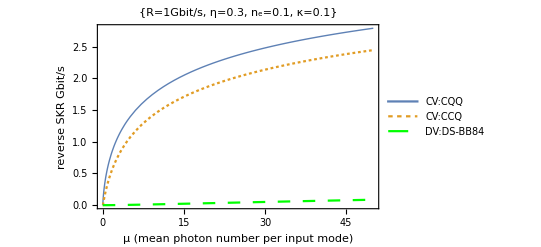

```mathematica
etaB=0.7;
Plot[{R Max[QCQSKRrev/.{κ->0.001/(1-etaB),ne->0.01,η-> etaB,μ->NS},0]/2,R Max[CCQSKRrev/.{κ->0.001/(1-etaB),ne->0.01,η-> etaB,μ->NS},0]/2,JeffSKR/.{ND->0.01 ,etaE->0.001}},{NS,0,50},FrameLabel->{"μ (mean photon number per input mode)","reverse SKR Gbit/s"} ,PlotLabel->{"R=1Gbit/s, η=0.3, n_e=0.1, κ=0.1"},Frame-> True,PlotStyle->{Thick,Dashing[Tiny],{Dashing[Medium],Green}},PlotLegends->Placed[ {"CV:CQQ","CV:CCQ","DV:DS-BB84"},{Right, Center}]]
```

Max::nord: Invalid comparison with 0.00646567+0.000907585 ⅈ attempted.

Max::nord: Invalid comparison with 1.15937+0.00170059 ⅈ attempted.

General::stop: Further output of Max::nord will be suppressed during this calculation.

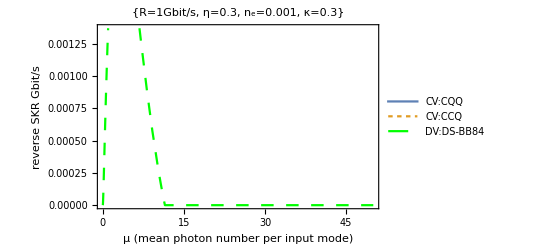

```mathematica
Plot[{R Max[QCQSKRrev/.{κ->0.2985/(1-etaB),ne->0.001,η-> etaB,μ->NS},0]/2,R Max[CCQSKRrev/.{κ->0.2985/(1-etaB),ne->0.001,η-> etaB,μ->NS},0]/2,JeffSKR/.{ND->0.001 *(1-etaB),etaE->0.2985}},{NS,0,50},FrameLabel->{"μ (mean photon number per input mode)","reverse SKR Gbit/s"} ,PlotLabel->{"R=1Gbit/s, η=0.3, n_e=0.001, κ=0.3"},Frame-> True,PlotStyle->{Thick,Dashing[Tiny],{Dashing[Medium],Green}},PlotLegends->Placed[ {"CV:CQQ","CV:CCQ","DV:DS-BB84"},{Right, Center}]]
```

```mathematica
etaB
```

0.005

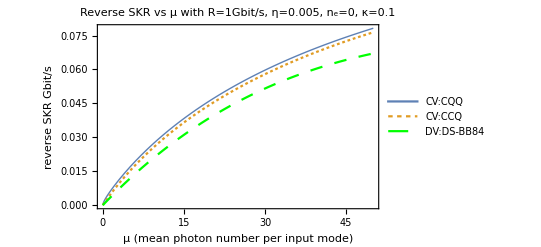

```mathematica
Plot[{R Max[QCQSKRrev/.{κ->0.01/(1-etaB),ne->10^-11,η-> etaB,μ->NS},0]/2,R Max[CCQSKRrev/.{κ->0.01/(1-etaB),ne->10^-11,η-> etaB,μ->NS},0]/2,JeffSKR/.{ND->10^-11 ,etaE->0.01}},{NS,0,50},FrameLabel->{"μ (mean photon number per input mode)","reverse SKR Gbit/s"} ,PlotLabel->"Reverse SKR vs μ with R=1Gbit/s, η=0.005, n_e=0, κ=0.1",Frame-> True,PlotStyle->{Thick,Dashing[Tiny],{Dashing[Medium],Green}},PlotLegends->Placed[ {"CV:CQQ","CV:CCQ","DV:DS-BB84"},{Right, Center}]]
```

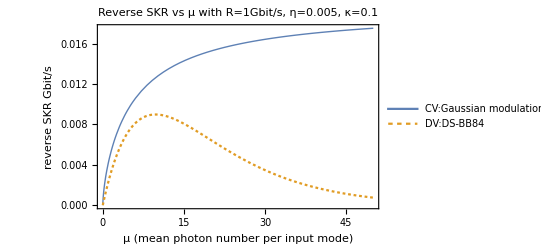

```mathematica
Plot[{R Max[QCQSKRrev/.{κ->0.1/(1-etaB),ne->10^-11,η-> etaB,μ->NS},0]/2,JeffSKR/.{ND->10^-11 ,etaE->0.1}},{NS,0,50},FrameLabel->{"μ (mean photon number per input mode)","reverse SKR Gbit/s"} ,PlotLabel->"Reverse SKR vs μ with R=1Gbit/s, η=0.005, κ=0.1",Frame-> True,PlotStyle->{Thick,Dashing[Tiny],{Dashing[Medium],Green}},PlotLegends->Placed[ {"CV:Gaussian modulation","DV:DS-BB84"},{Right, Center}]]
```

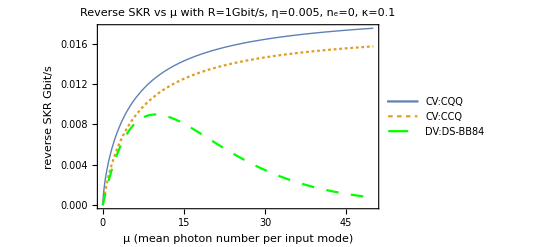

```mathematica
Plot[{R Max[QCQSKRrev/.{κ->0.1/(1-etaB),ne->10^-11,η-> etaB,μ->NS},0]/2,R Max[CCQSKRrev/.{κ->0.1/(1-etaB),ne->10^-11,η-> etaB,μ->NS},0]/2,JeffSKR/.{ND->10^-11 ,etaE->0.1}},{NS,0,50},FrameLabel->{"μ (mean photon number per input mode)","reverse SKR Gbit/s"} ,PlotLabel->"Reverse SKR vs μ with R=1Gbit/s, η=0.005, n_e=0, κ=0.1",Frame-> True,PlotStyle->{Thick,Dashing[Tiny],{Dashing[Medium],Green}},PlotLegends->Placed[ {"CV:CQQ","CV:CCQ","DV:DS-BB84"},{Right, Center}]]
```

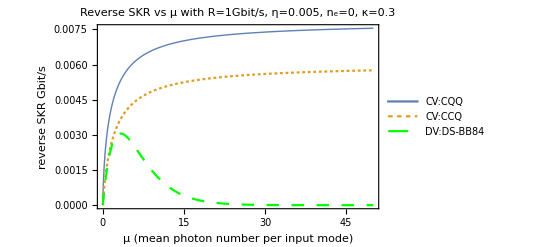

```mathematica
Plot[{R Max[QCQSKRrev/.{κ->0.2985/(1-etaB),ne->10^-11,η-> etaB,μ->NS},0]/2,R Max[CCQSKRrev/.{κ->0.2985/(1-etaB),ne->10^-11,η-> etaB,μ->NS},0]/2,JeffSKR/.{ND->10^-11,etaE->0.2985}},{NS,0,50},FrameLabel->{"μ (mean photon number per input mode)","reverse SKR Gbit/s"} ,PlotLabel->"Reverse SKR vs μ with R=1Gbit/s, η=0.005, n_e=0, κ=0.3",Frame-> True,PlotStyle->{Thick,Dashing[Tiny],{Dashing[Medium],Green}},PlotLegends->Placed[ {"CV:CQQ","CV:CCQ","DV:DS-BB84"},{Right, Center}]]
```

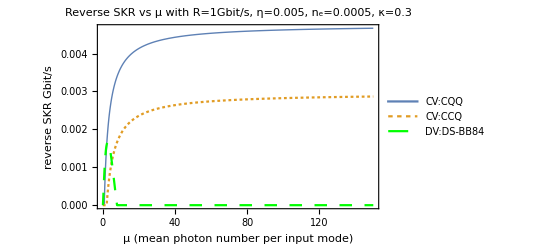

```mathematica
etaB=0.005;
Plot[{R Max[QCQSKRrev/.{κ->0.2985/(1-etaB),ne->5*10^-4,η-> etaB,μ->NS},0]/2,R Max[CCQSKRrev/.{κ->0.2985/(1-etaB),ne->5*10^-4,η-> etaB,μ->NS},0]/2,JeffSKR/.{ND->5*10^-4,etaE->0.2985}},{NS,0,150},FrameLabel->{"μ (mean photon number per input mode)","reverse SKR Gbit/s"} ,PlotLabel->"Reverse SKR vs μ with R=1Gbit/s, η=0.005, n_e=0.0005, κ=0.3",Frame-> True,PlotStyle->{Thick,Dashing[Tiny],{Dashing[Medium],Green}},PlotLegends->Placed[ {"CV:CQQ","CV:CCQ","DV:DS-BB84"},{Right, Bottom}]]
```

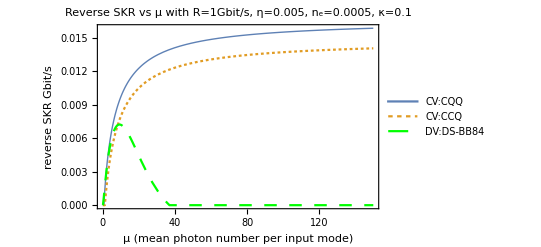

```mathematica
etaB=0.005;
Plot[{R Max[QCQSKRrev/.{κ->0.1/(1-etaB),ne->5*10^-4,η-> etaB,μ->NS},0]/2,R Max[CCQSKRrev/.{κ->0.1/(1-etaB),ne->5*10^-4,η-> etaB,μ->NS},0]/2,JeffSKR/.{ND->5*10^-4,etaE->0.1}},{NS,0,150},FrameLabel->{"μ (mean photon number per input mode)","reverse SKR Gbit/s"} ,PlotLabel->"Reverse SKR vs μ with R=1Gbit/s, η=0.005, n_e=0.0005, κ=0.1",Frame-> True,PlotStyle->{Thick,Dashing[Tiny],{Dashing[Medium],Green}},PlotLegends->Placed[ {"CV:CQQ","CV:CCQ","DV:DS-BB84"},{Right, Center}]]
```